Photon burst identification and manipulation of the burst list

Load some datapaclet:Fretica/tutorial/PhotonBurstIdentificationAndManipulationOfTheBurstList#185255028 | Manipulation of the burst list and of the TTTR data paclet:Fretica/tutorial/PhotonBurstIdentificationAndManipulationOfTheBurstList#20261581
Burst Identificationpaclet:Fretica/tutorial/PhotonBurstIdentificationAndManipulationOfTheBurstList#313146471 | FGetBurstListSize[]paclet:Fretica/tutorial/PhotonBurstIdentificationAndManipulationOfTheBurstList#447855938
Burst asymmetry cutpaclet:Fretica/tutorial/PhotonBurstIdentificationAndManipulationOfTheBurstList#592067340 |

```mathematica
Needs["Fretica`"]
```

Load some data

```mathematica
(*typical settings for a two channel FRET measurement*)
FEnablePie[False];
FSetFRETRoutes[{"A","D"}](* detector1: acceptor, detector2: donor*)
FSetRCM[{{1,-0.06},{-0.008,1.25}}];(*γ=1.25, Subscript[β, D->A]=0.06, Subscript[β, A->D]=0.008*)
FSetDirectAcceptorExcitation[0.05];
FOpenTTTR[$FreticaExamples<>"\\1.00GdmClA.t3r"] (*Csp near the folding midpoint*)
FDetermineBackground[](*returns estimated background rates in counts per seconds*)
```

1

{2751.13,3067.25,0.,0.,0.,0.}

Burst Identification

### Δt-method, FFindBurstsDeltaT

```mathematica
?FFindBurstsDeltaT
```

-Graphics-

{2751.13,3067.25,0.,0.,0.,0.}

18372

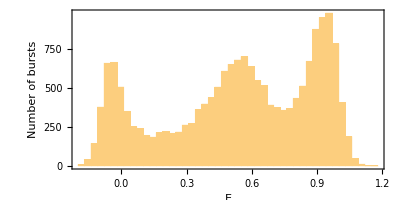

```mathematica
FPCH[1.]
FDetermineBackground[]
FFindBurstsDeltaT[0.00015,50,10000]
FParamHisto["E",{-0.2,1.2,0.03}]
```

```mathematica
FGetBurstListSize[]
```

18372

### "Binning"-method, FFindBurstsFromTimeBinnedData

```mathematica
?FFindBurstsFromTimeBinnedData
```

4063

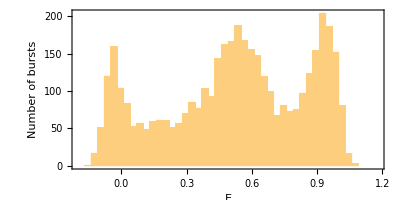

```mathematica
FFindBurstsFromTimeBinnedData[1,20,100,10000]
FParamHisto["E",{-0.2,1.2,0.03}]
```

64448

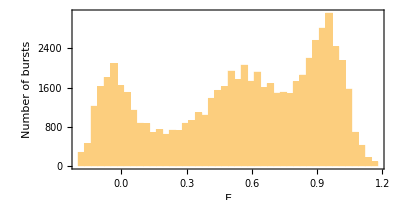

```mathematica
FFindBurstsFromTimeBinnedData[1,20,0,10000,FCombineContiguousBins->False]
FParamHisto["E",{-0.2,1.2,0.03}]
```

#### Example: Systematic variation of nmin and Δtmax

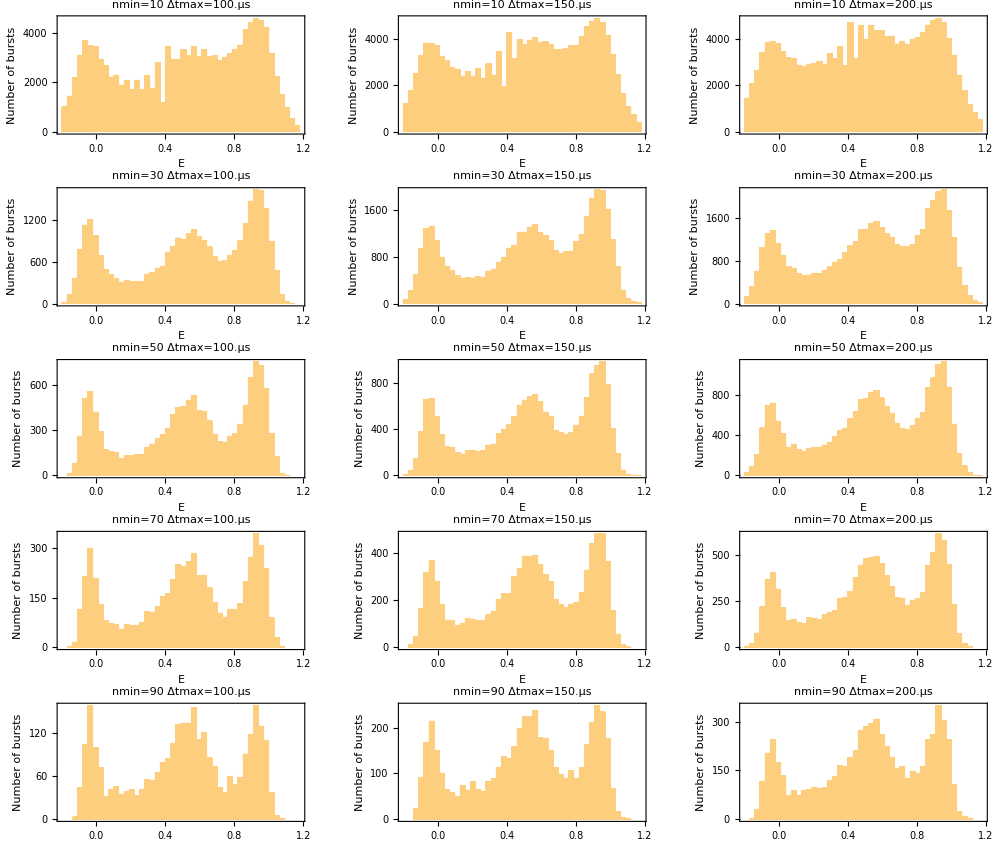

```mathematica
GraphicsGrid[Table[
(FFindBurstsDeltaT[dtmax,nmin,10000];
FParamHisto["E",{-0.2,1.2,0.03},
PlotLabel->"nmin="<>ToString[nmin]<>" Δtmax="<>ToString[dtmax 10.^6]<>"μs",ImageSize->200])
,{nmin,10,100,20},{dtmax,0.0001,0.0002,0.00005}],ImageSize->1000]
```

### FSetBurstList

Fretica allows to set the burst list manually using FSetBurstList.

```mathematica
?FSetBurstList
```

Burst asymmetry cut

```mathematica
?FBurstAsymmetry
```

```mathematica
?FCutAsymmetricBursts
```

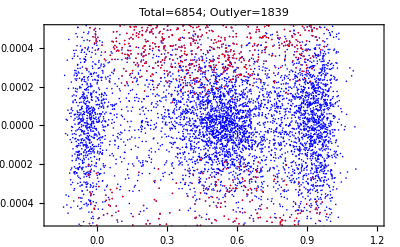
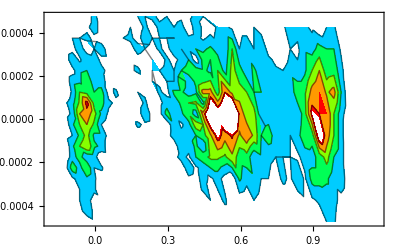
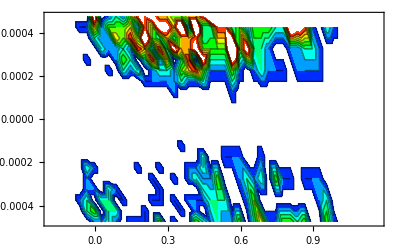

```mathematica
FBurstAsymmetry[{-0.2,1.2,0.03},{-0.0005,0.0005,0.00005},2.]
```

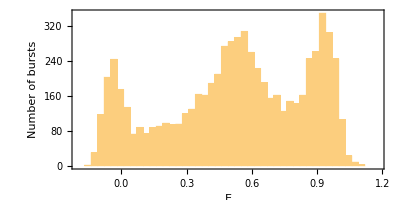

1

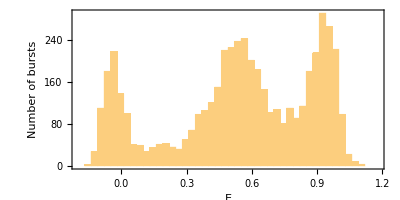

```mathematica
FParamHisto["E",{-0.2,1.2,0.03}]
FCutAsymmetricBursts[2.]
FParamHisto["E",{-0.2,1.2,0.03}]
```

Manipulation of the burst list and of the TTTR data

#### FSplitBursts, FExpandBurstsSymmetrically, FUpdateBurstCounts, FDeleteSelectedBursts, FDeleteNoneSelectedBursts, FReduceToBurstPhotons

```mathematica
?FSplitBursts
```

```mathematica
?FExpandBurstsSymmetrically
```

```mathematica
?FUpdateBurstCounts
```

```mathematica
?FDeleteSelectedBursts
```

```mathematica
?FDeleteNonSelectedBursts
```

```mathematica
?FReduceToBurstPhotons
```

FGetBurstListSize[]

```mathematica
?FGetBurstListSize
```

```mathematica
FGetBurstListSize[]
```

5015

| Related Guides
▪Fretica